```mathematica
Needs["Quantum`Computing`"]
```

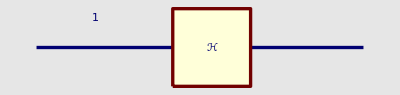

-Graphics3D-

(|0⟩⟨0|)/(√2)+(|1⟩⟨0|)/(√2)+(|0⟩⟨1|)/(√2)-(|1⟩⟨1|)/(√2)

|   Input |   Output
0 | |0⟩ | (|0⟩)/(√2)+(|1⟩)/(√2)
1 | |1⟩ | (|0⟩)/(√2)-(|1⟩)/(√2)

(1/(√2) | 1/(√2)
1/(√2) | -1/(√2))

```mathematica
circuitexpr := Subscript[ℋ, OverHat[1]]
QuantumPlot[circuitexpr]
QuantumPlot3D[circuitexpr]
TraditionalForm[QuantumEvaluate[circuitexpr]]
TraditionalForm[QuantumTableForm[circuitexpr]]
QuantumMatrixForm[circuitexpr]
```

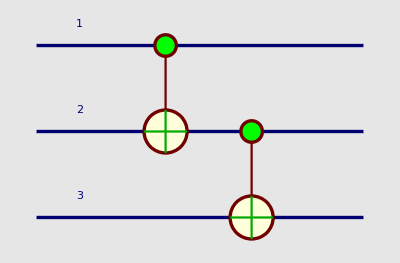

-Graphics3D-

|   Input |   Output
0 | |000⟩ | |000⟩
1 | |001⟩ | |001⟩
2 | |010⟩ | |011⟩
3 | |011⟩ | |010⟩
4 | |100⟩ | |111⟩
5 | |101⟩ | |110⟩
6 | |110⟩ | |100⟩
7 | |111⟩ | |101⟩

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)

```mathematica
circuitexpr := (𝒞^{OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[3]]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]
QuantumPlot[circuitexpr]
QuantumPlot3D[circuitexpr]
TraditionalForm[QuantumTableForm[circuitexpr]]
QuantumMatrixForm[circuitexpr]
```

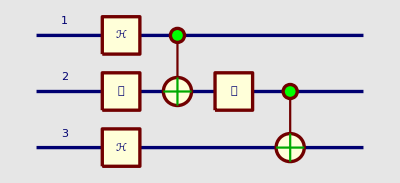

-Graphics3D-

|   Input |   Output
0 | |000⟩ | -1/2 ⅈ |000⟩-1/2 ⅈ |001⟩+1/2 ⅈ |110⟩+1/2 ⅈ |111⟩
1 | |001⟩ | -1/2 ⅈ |000⟩+1/2 ⅈ |001⟩-1/2 ⅈ |110⟩+1/2 ⅈ |111⟩
2 | |010⟩ | 1/2 ⅈ |010⟩+1/2 ⅈ |011⟩-1/2 ⅈ |100⟩-1/2 ⅈ |101⟩
3 | |011⟩ | -1/2 ⅈ |010⟩+1/2 ⅈ |011⟩-1/2 ⅈ |100⟩+1/2 ⅈ |101⟩
4 | |100⟩ | -1/2 ⅈ |000⟩-1/2 ⅈ |001⟩-1/2 ⅈ |110⟩-1/2 ⅈ |111⟩
5 | |101⟩ | -1/2 ⅈ |000⟩+1/2 ⅈ |001⟩+1/2 ⅈ |110⟩-1/2 ⅈ |111⟩
6 | |110⟩ | 1/2 ⅈ |010⟩+1/2 ⅈ |011⟩+1/2 ⅈ |100⟩+1/2 ⅈ |101⟩
7 | |111⟩ | -1/2 ⅈ |010⟩+1/2 ⅈ |011⟩+1/2 ⅈ |100⟩-1/2 ⅈ |101⟩

```mathematica
circuitexpr := (𝒞^{OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[3]]]·Subscript[𝒴, OverHat[2]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·Subscript[ℋ, OverHat[3]]·Subscript[𝒳, OverHat[2]]·Subscript[ℋ, OverHat[1]]
QuantumPlot[circuitexpr]
QuantumPlot3D[circuitexpr]
TraditionalForm[QuantumTableForm[circuitexpr]]
```